# Avaliação do Campo Crítico em Circuito de 230 kV

## Antonio C. S. Lima

Este documento apresenta o cálculo do campo crítico nos condutores para um circuito de 230kV 
Não comtempla os cabos PR

## Inicialização

```mathematica
SetDirectory[NotebookDirectory[]]
(*SetDirectory["B:\\otlin"]*)
```

/Users/acsl/Dropbox/UFRJ/cursos/EEE457-Transmissão_Energia_Elétrica/arquivos_Mma_EEE457

```mathematica
SetOptions[{Plot,LogPlot,LogLinearPlot,LogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,PlotStyle-> Thick,
Axes-> False,Frame-> True];
```

```mathematica
dadoscond=Import["condcompleta.txt","Table"];
camp=Import["campos.txt","CSV"];
```

## Variáveis obtidas do programa de otimização dos condutores

```mathematica
nfase=3;
ns=2;
npr=2;
ncond=IntegerPart[ns*nfase+npr]
```

8

### Dados do Meio

#### Ar

```mathematica
μo=4.0*Pi*10^-7;
ϵo=8.854 10^-12;
```

#### Solo

```mathematica
σearth=1.0 10^-3;                                 (* ⟹ Condutividade do Solo ⟸ *)
```

### Dados do condutor

```mathematica
Nome=ToUpperCase["rail"];
```

```mathematica
pos=Module[{posicao},posicao=If[NumberQ[Position[dadoscond,Nome][[1,1]]],Position[dadoscond,Nome][[1,1]],1];If[NumberQ[Position[dadoscond,Nome][[1,1]]],,Print["O condutor especificado não exite na tabela, verifique o nome digitado. Para não ocorrer erros nos cálculos foram utilizados os valores do condutor Owl"]];Return[posicao]];

{nome,MCM,NAl,DAl,NACO,DACO,secAl,secACO,Dcond,DALMA,PesoAl,PesoACO,Massa,CargaRupturaClasseA,CargaRupturaClasseB,Ampacidade,RMG,ResCC,ResAC,Xind,Xcap}=dadoscond[[pos]];

Table[Print[i,")  ",camp[[i,1]], " = ",dadoscond[[pos,i]]],{i,1,Length[camp]}];
```

Return[45]

1)  Nome comercial = RAIL

2)  Bitola (MCM) = 954

3)  Num. de Fios de Al. = 45

4)  Diâmetro dos Fios de Al. (mm) = 3.698

5)  Num. de Fios de Aço = 7

6)  Diâmetro dos Fios de Aço (mm) = 2.466

7)  Seção transversal de Al (mm^2) = 483.32

8)  Seção transversal do cond. (mm^2) = 516.8

9)  Diâmetro do cond. (mm) = 29.59

10)  Diâmetro da Alma de Aço (mm) = 7.4

11)  Peso Nominal do Al (aprox.) (kg/km) = 1339.1

12)  Peso nominal do Aço (aprox.) (kg/km) = 261.1

13)  Massa (aprox.) (kg/km) = 1600.2

14)  Carga de ruptura (Classe A) (kgf) = 11764

15)  Carga de ruptura (Classe B) (kgf) = 11535

16)  Ampacidade (A) = 970

17)  Raio médio geométrico (m) = 0.01174

18)  Resistência elétrica máxima CC a 20.baC (Ohm/km) = 0.06

19)  Resistência elétrica máxima CA @ 60 Hz e 75.baC (Ohm/km) = 0.073

20)  Reatância indutiva (Ohm/km) = 0.3352

21)  Reatância capacitiva (Mohm/km) = 0.2011

### Dados dos Condutores

```mathematica
r0=(dadoscond[[pos,10]]/2)*10^-3;   (* ⟹ [m] ⟸ *)
r1=(dadoscond[[pos,9]]/2)*10^-3;

ρAl=0.028264;    (* resistividade ⟹ Ω × mm^2/ m ⟸ *)
ρAlmetro=0.028264*10^-6;    (* ⟹ Ω × m ⟸ *)

Rdcϕ=(dadoscond[[pos,18]])*10^-3;  (* ⟹ [Ω/m] ⟸⟹ @ 20^o ⟸*)
ρϕ=Rdcϕ*Pi*(r1^2-r0^2);

σϕ=(1/ρAlmetro)*(dadoscond[[pos,3]]*(dadoscond[[pos,4]]*10^-3/2)^2)/(r1^2-r0^2);
```

```mathematica
svao=0.45; (* comprimento do vão em [km] *)
T=dadoscond[[pos,15]];
W=dadoscond[[pos,13]];
H=0.24*T;
Ccat=H/W;
(*flecha em metro
flechacond=1000*Ccat*(Cosh[svao/(2*Ccat)]-1)*)
flechacond=1000*Ccat*(Cosh[svao/(2*Ccat)]-1)
```

14.6519

### Dados dos Cabos PR

```mathematica
rpr=4.57*10^-3; (* [m] *)

Rdcpr=4.19*10^-3;

ρpr=Rdcpr*Pi*rpr^2;

σpr=1/ρpr;

μpr=80*μo;
```

```mathematica
Tpr=6980; (*{kgf]*)
Wpr=410; (*[kg/km]*)
Hpr=0.25*Tpr;
Ccatpr=Hpr/Wpr;
(*flecha em metro*)
flechapr=1000*Ccatpr*(Cosh[svao/(2*Ccatpr)]-1)
```

5.94873

#### Lista de raios dos condutores

```mathematica
r=Join[Table[r1,{ncond-npr}],Table[rpr,{npr}]];
```

## Coordenadas dos condutores

```mathematica
varx=Array[ToExpression[StringJoin["coorx",ToString[#]]]&,ncond];
vary=Array[ToExpression[StringJoin["coory",ToString[#]]]&,ncond];
```

```mathematica
b=.457; (* espacamento entre os feixes *)
h=14.651852276415907; (*flecha dos condutores *)
xc={ -7.85-b/2, -7.85+b/2,-b/2,b/2,7.85-b/2, 7.86+b/2, -7,7};
yc={7.5+h,7.5+h,7.5+h,7.5+h,7.5+h,7.5+h,7.5+h+5.3,7.5+h+5.3};
```

```mathematica
yc
```

{22.1519,22.1519,22.1519,22.1519,22.1519,22.1519,27.4519,27.4519}

```mathematica
yini2=Table[If[i<=ncond-npr,yc[[i]]-flechacond,yc[[i]]-flechapr],{i,ncond}];
```

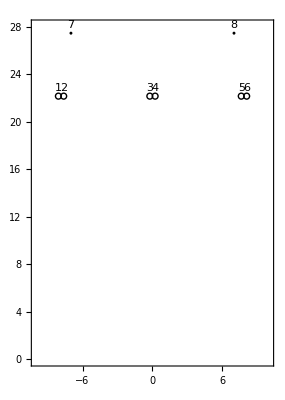

```mathematica
mostra=Table[If[i≤ Length[xc]-2,
Circle[{xc[[i]],yc[[i]]},0.25],
Disk[{xc[[i]],yc[[i]]},.125]],
{i,1,Length[xc]}];
num=Table[Text[i,{xc[[i]],.65+yc[[i]]}],{i,1,8}];

Show[{Graphics[num],Graphics[mostra]},Frame-> True,PlotRange->{{-10,10},{0,28.0}}]
```